-Graphics3D-

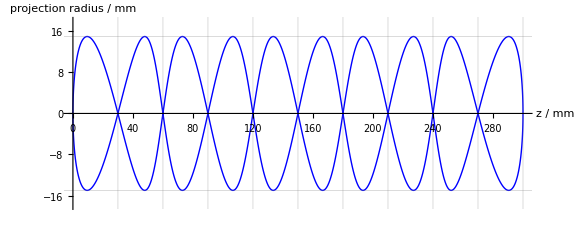

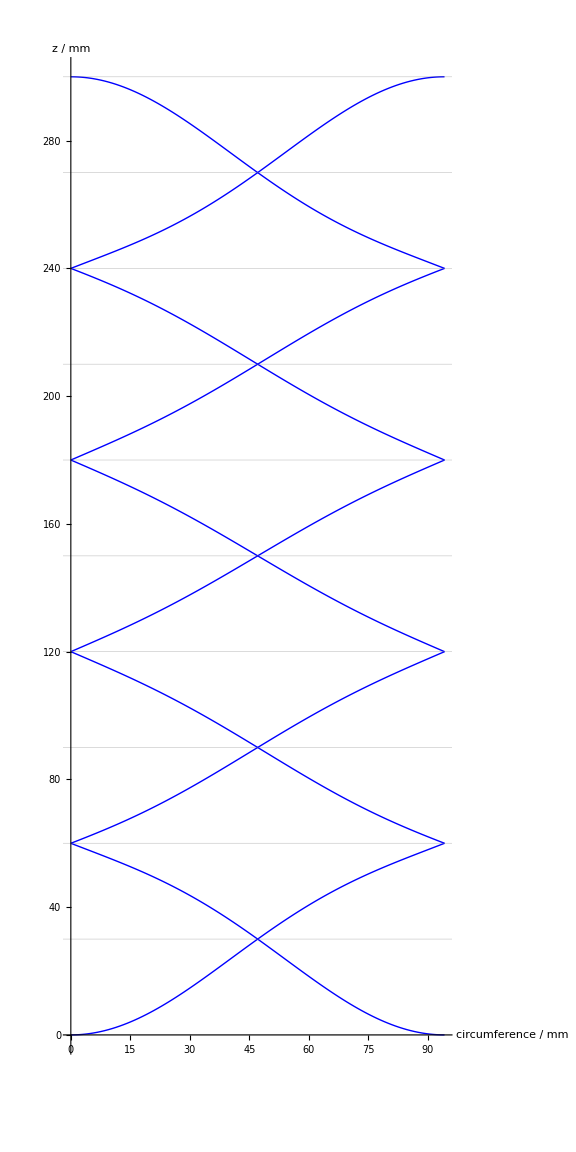

j | u1 | u2 | z(u1) | z(u2) | z(u1) - j dz
0 | 0 | 10 | 0 | 0 | 0
1 | 1/2 | 19/2 | 30. | 30. | 0
2 | 1 | 9 | 60. | 60. | 0
3 | 3/2 | 17/2 | 90. | 90. | 0
4 | 2 | 8 | 120. | 120. | 0
5 | 5/2 | 15/2 | 150. | 150. | 0
6 | 3 | 7 | 180. | 180. | 0
7 | 7/2 | 13/2 | 210. | 210. | 0
8 | 4 | 6 | 240. | 240. | 0
9 | 9/2 | 11/2 | 270. | 270. | 0
10 | 5 | 5 | 300. | 300. | 0

```mathematica
ClearAll["Global`*"];

(* =========================基本参数=========================*)

r0=15.;(*槽中心线所在圆柱半径，单位 mm，可按图纸修改*)dz=30.;(*相邻自交/控制点的 z 向距离，单位 mm*)m=10;(*z 向分段数；总有效槽长 len=m dz*)len=m dz;(*有效槽长，这里为 300 mm*)phi0=0.;(*初始相位角，可调*)(*说明：u 是绕轴转过的圈数参数。0≤u≤m 表示完整一来一回。0≤u≤m/2 是从左到右；m/2≤u≤m 是从右到左。*)(* =========================构造全局多项式 F 不是样条，不是分段曲线=========================*)xNodes=N@Table[(1-Cos[Pi j/m])/2,{j,0,m}];
yNodes=N@Table[j/m,{j,0,m}];

baryWeights=Table[1/Product[xNodes[[i]]-xNodes[[k]],{k,DeleteCases[Range[m+1],i]}],{i,1,m+1}];

F[w_?NumericQ]:=Module[{d,hit},d=w-xNodes;
hit=FirstPosition[d,x_/;Abs[x]<10^-10,Missing["NotFound"]];
If[hit=!=Missing["NotFound"],yNodes[[hit[[1]]]],Total[baryWeights*yNodes/d]/Total[baryWeights/d]]];

wOfU[u_?NumericQ]:=(1-Cos[2 Pi u/m])/2;

zOfU[u_?NumericQ]:=len F[wOfU[u]];

pt[u_?NumericQ]:={r0 Cos[2 Pi u+phi0],r0 Sin[2 Pi u+phi0],zOfU[u]};

(* =========================3D 效果图=========================*)

curve3D=ParametricPlot3D[pt[u],{u,0,m},PlotStyle->{Blue,Thick},PlotPoints->800,MaxRecursion->2,Mesh->None];

cylinder=Graphics3D[{Opacity[0.10],LightGray,Cylinder[{{0,0,0},{0,0,len}},r0]}];

crossPts=Table[pt[j/2],{j,1,m-1}];
endPts={pt[0],pt[m/2],pt[m]};

pts3D=Graphics3D[{Red,PointSize[0.018],Point[crossPts],Black,PointSize[0.020],Point[endPts]}];

main3D=Show[cylinder,curve3D,pts3D,BoxRatios->{1,1,5},AxesLabel->{"x / mm","y / mm","z / mm"},PlotRange->All,ImageSize->Large];

main3D

(*正视图*)
sideView=ParametricPlot[{zOfU[u],r0 Sin[2 Pi u+phi0]},{u,0,m},PlotStyle->{Blue,Thick},PlotPoints->1000,MaxRecursion->2,AxesLabel->{"z / mm","projection radius / mm"},PlotRange->{{0,len},{-1.2 r0,1.2 r0}},GridLines->{Range[0,len,dz],{-r0,0,r0}},ImageSize->Large];

sideView


(*圆柱展开图*)


flatPieces=Table[ParametricPlot[{2 Pi r0 (u-k),zOfU[u]},{u,k,k+1},PlotStyle->{Blue,Thick},PlotPoints->100,MaxRecursion->1],{k,0,m-1}];

flatView=Show[flatPieces,AxesLabel->{"circumference / mm","z / mm"},PlotRange->{{0,2 Pi r0},{0,len}},GridLines->{None,Range[0,len,dz]},AspectRatio->2,ImageSize->Large];

flatView

(*检查 z 向等分是不是严格为 30*)

checkTable=Table[{j,j/2,m-j/2,Chop[zOfU[j/2]],Chop[zOfU[m-j/2]],Chop[zOfU[j/2]-j dz]},{j,0,m}];

Grid[Prepend[checkTable,{"j","u1","u2","z(u1)","z(u2)","z(u1) - j dz"}],Frame->All]

(*
如果你图纸里的 30 是螺距 P，而不是相邻自交点的 z 向间距，那么通常应改成：
dz=15.;
m=20;

因为左右反向螺旋相交时，交点的 z 向间距通常是半个螺距。但如果你明确要求“自交点之间就是 30”，就保持上面默认的：
dz=30.;
m=10;

*)
```